```mathematica
Length[f0cf1500]
```

11

{a→0.000974089,b→0.000219004,c→0.000435689}

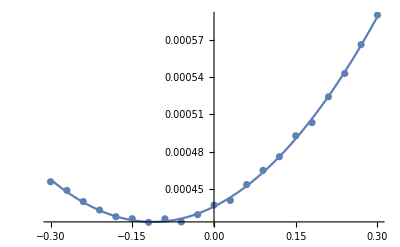

{x→-0.349423}

{x→0.124593}

```mathematica
f0cf1500=10^12{-3*10^-13,-2.7*10^-13,-2.4*10^-13,-2.1*10^-13,-1.8*10^-13,-1.5*10^-13,-1.2*10^-13,-9*10^-14,-6*10^-14,-3*10^-14,0.0,3*10^-14,6*10^-14,9*10^-14,1.2*10^-13,1.5*10^-13,1.8*10^-13,2.1*10^-13,2.4*10^-13,2.7*10^-13,3*10^-13};
f0cs1500={0.0017118,0.0017019,0.0016938,0.0016883,0.0016839,0.001684,0.0016827,0.0016868,0.0016914,0.0016994,0.0017092,0.0017218,0.0017355,0.0017524,0.0017719,0.0017938,0.0018175,0.0018421,0.0018705,0.0019012,0.0019325};
f0n1500={79870,79110,77898,76931,76172,75890,75416,75739,75092,75767,76694,76777,78387,79599,80584,82427,83103,85379,87102,89373,91624};
f0cs1500f=f0cs1500*f0n1500/300000;
f0fit1500=FindFit[Transpose[{f0cf1500,f0cs1500f}],a x^2+b x+c,{a,b,c},x]
Show[Plot[a x^2+b x+c/. f0fit1500,{x,f0cf1500[[1]],f0cf1500[[21]]}],ListPlot[Transpose[{f0cf1500,f0cs1500f}]]]
Print[FindRoot[2==√2 √ll √((a x^2+b x+ c)Log[1+(a x^2+b x)/c]-(a x^2+b x))/.ll->1000000/.f0fit1500,{x,-1.1}]];
Print[FindRoot[2==√2 √ll √((a x^2+b x+ c)Log[1+(a x^2+b x)/c]-(a x^2+b x))/.ll->1000000/.f0fit1500,{x,0.1}]];
```

```mathematica
{x->-0.3549242886696732}
```

```mathematica
{x->0.13395894741460837}
```

```mathematica
f0cs1500f=f0cs1500*f0n1500/300000
```

{0.000811239,0.000804108,0.000797046,0.000791385,0.000781706,0.000788129,0.000784564,0.000789057,0.000788305,0.000797404,0.000800265,0.000807507,0.00082103,0.000833459,0.000846419,0.000863266,0.000879307,0.000898963,0.000918278,0.000940403,0.000966611}

{a→1.38727,b→0.00246063,c→0.0000417479}

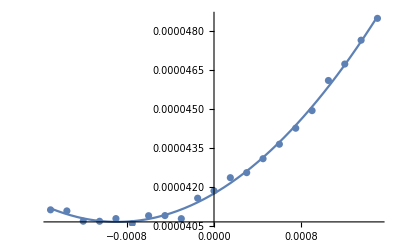

{x→-0.00283106}

{x→0.00105733}

```mathematica
f0cf5000=10^12{-1.5*10^-15,-1.35*10^-15,-1.2*10^-15,-1.05*10^-15,-9*10^-16,-7.5*10^-16,-6*10^-16,-4.5*10^-16,-3*10^-16,-1.5*10^-16,0.0,1.5*10^-16,3*10^-16,4.5*10^-16,6*10^-16,7.5*10^-16,9*10^-16,1.05*10^-15,1.2*10^-15,1.35*10^-15,1.5*10^-15};
f0cs5000={0.00015158,0.00015158,0.00015158,0.00015149,0.00015156,0.00015186,0.00015207,0.0001523,0.00015272,0.00015321,0.0001538,0.00015454,0.00015513,0.000156,0.00015691,0.00015789,0.00015891,0.00016004,0.00016122,0.00016262,0.00016391};
f0n5000={81384,81302,80519,80563,80728,80195,80677,80565,80109,81395,81634,82227,82289,82861,83446,84098,84837,86410,86955,87899,88745};
f0cs5000f=f0cs5000*f0n5000/300000;
f0fit5000=FindFit[Transpose[{f0cf5000,f0cs5000f}],a x^2+b x+c,{a,b,c},x]
Show[Plot[a x^2+b x+c/. f0fit5000,{x,f0cf5000[[1]],f0cf5000[[21]]}],ListPlot[Transpose[{f0cf5000,f0cs5000f}]]]
Print[FindRoot[2==√2 √ll √((a x^2+b x+ c)Log[1+(a x^2+b x)/c]-(a x^2+b x))/.ll->10000000/.f0fit5000,{x,-0.1}]];
Print[FindRoot[2==√2 √ll √((a x^2+b x+ c)Log[1+(a x^2+b x)/c]-(a x^2+b x))/.ll->10000000/.f0fit5000,{x,0.1}]];
```

```mathematica
{x->-0.0028310553005673044}
```

```mathematica
{x->0.001057331216010425}
```

```mathematica
{x->-0.002841508262336805}
```

```mathematica
{x->0.0010557140293872517}
```

{a→9.96679,b→0.00470672,c→0.0000190974}

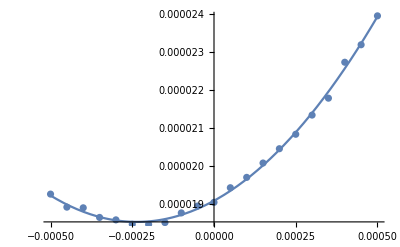

{x→-0.000818934}

{x→0.000346694}

```mathematica
f0cf7000=10^12{-5*10^-16,-4.5*10^-16,-4*10^-16,-3.5*10^-16,-3*10^-16,-2.5*10^-16,-2*10^-16,-1.5*10^-16,-1*10^-16,-5*10^-17,0.0,5*10^-17,1*10^-16,1.5*10^-16,2*10^-16,2.5*10^-16,3*10^-16,3.5*10^-16,4*10^-16,4.5*10^-16,5*10^-16};
f0cs7000={7.7706*10^-05,7.7517*10^-05,7.7427*10^-05,7.7379*10^-05,7.7233*10^-05,7.7351*10^-05,7.7403*10^-05,7.7583*10^-05,7.7789*10^-05,7.8052*10^-05,7.8459*10^-05,7.8973*10^-05,7.9336*10^-05,7.9997*10^-05,8.0637*10^-05,8.1322*10^-05,8.2133*10^-05,8.2918*10^-05,8.3834*10^-05,8.475*10^-05,8.5749*10^-05};
f0n7000={74406,73261,73277,72342,72230,71668,71608,71628,72419,72869,72863,73848,74539,75338,76140,76900,77983,78853,81371,82120,83820};
f0cs7000f=f0cs7000*f0n7000/300000;
f0fit7000=FindFit[Transpose[{f0cf7000,f0cs7000f}],a x^2+b x+c,{a,b,c},x]
Show[Plot[a x^2+b x+c/. f0fit7000,{x,f0cf7000[[1]],f0cf7000[[21]]}],ListPlot[Transpose[{f0cf7000,f0cs7000f}]]]
Print[FindRoot[2==√2 √ll √((a x^2+b x+ c)Log[1+(a x^2+b x)/c]-(a x^2+b x))/.ll->10000000/.f0fit7000,{x,-0.1}]];
Print[FindRoot[2==√2 √ll √((a x^2+b x+ c)Log[1+(a x^2+b x)/c]-(a x^2+b x))/.ll->10000000/.f0fit7000,{x,0.1}]];
```

```mathematica
{x->-0.0008189336104687563}
```

```mathematica
{x->0.00034669358742329384}
```

{a→2272.56,b→0.137293,c→0.000019141}

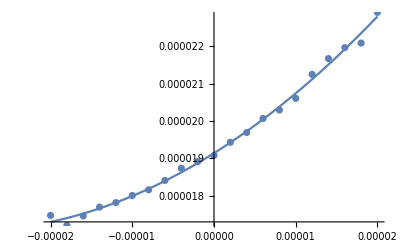

{x→-0.0000766719}

{x→0.0000162586}

```mathematica
f9cf7000=10^12{-2*10^-17,-1.8*10^-17,-1.6*10^-17,-1.4*10^-17,-1.2*10^-17,-1*10^-17,-8*10^-18,-6*10^-18,-4*10^-18,-2*10^-18,0.0,2*10^-18,4*10^-18,6*10^-18,8*10^-18,1*10^-17,1.2*10^-17,1.4*10^-17,1.6*10^-17,1.8*10^-17,2*10^-17};
f9cs7000={7.4845*10^-05,7.5122*10^-05,7.5498*10^-05,7.5824*10^-05,7.6023*10^-05,7.6463*10^-05,7.6773*10^-05,7.7205*10^-05,7.7566*10^-05,7.7973*10^-05,7.8459*10^-05,7.9027*10^-05,7.9407*10^-05,8.0021*10^-05,8.059*10^-05,8.1152*10^-05,8.1822*10^-05,8.2374*10^-05,8.3022*10^-05,8.3664*10^-05,8.4348*10^-05};
f9n7000={70052,68729,69394,70027,70321,70662,70972,71547,72476,72775,72964,73766,74403,75241,75552,76180,77909,78917,79363,79192,81467};
f9cs7000f=f9cs7000*f9n7000/300000;
f9fit7000=FindFit[Transpose[{f9cf7000,f9cs7000f}],a x^2+b x+c,{a,b,c},x]
Show[Plot[a x^2+b x+c/. f9fit7000,{x,f9cf7000[[1]],f9cf7000[[21]]}],ListPlot[Transpose[{f9cf7000,f9cs7000f}]]]
Print[FindRoot[2==√2 √ll √((a x^2+b x+ c)Log[1+(a x^2+b x)/c]-(a x^2+b x))/.ll->10000000/.f9fit7000,{x,-0.1}]];
Print[FindRoot[2==√2 √ll √((a x^2+b x+ c)Log[1+(a x^2+b x)/c]-(a x^2+b x))/.ll->10000000/.f9fit7000,{x,0.1}]];
```

{a→942.404,b→0.0219567,c→4.64568×10^-6}

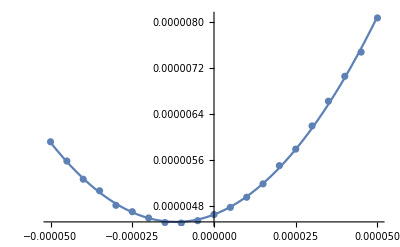

{x→-0.000052286}

{x→0.0000289873}

```mathematica
f0cf15000=10^12{-5*10^-17,-4.5*10^-17,-4*10^-17,-3.5*10^-17,-3*10^-17,-2.5*10^-17,-2*10^-17,-1.5*10^-17,-1*10^-17,-5*10^-18,6.162976*10^-33,5*10^-18,1*10^-17,1.5*10^-17,2*10^-17,2.5*10^-17,3*10^-17,3.5*10^-17,4*10^-17,4.5*10^-17,5*10^-17};
f0cs15000={1.8428*10^-05,1.7999*10^-05,1.7659*10^-05,1.7383*10^-05,1.7138*10^-05,1.6977*10^-05,1.686*10^-05,1.683*10^-05,1.6862*10^-05,1.6935*10^-05,1.7092*10^-05,1.7317*10^-05,1.7577*10^-05,1.7919*10^-05,1.8336*10^-05,1.8804*10^-05,1.9328*10^-05,1.9924*10^-05,2.058*10^-05,2.1291*10^-05,2.2089*10^-05};
f0n15000={96288,92982,89390,87335,84146,82974,81607,80341,80026,80410,81559,82651,84444,86733,89958,92319,96096,99705,102862,105373,109654};
f0cs15000f=f0cs15000*f0n15000/300000;
f0fit15000=FindFit[Transpose[{f0cf15000,f0cs15000f}],a x^2+b x+c,{a,b,c},x]
Show[Plot[a x^2+b x+c/. f0fit15000,{x,f0cf15000[[1]],f0cf15000[[21]]}],ListPlot[Transpose[{f0cf15000,f0cs15000f}]]]
Print[FindRoot[2==√2 √ll √((a x^2+b x+ c)Log[1+(a x^2+b x)/c]-(a x^2+b x))/.ll->10000000/.f0fit15000,{x,-0.1}]];
Print[FindRoot[2==√2 √ll √((a x^2+b x+ c)Log[1+(a x^2+b x)/c]-(a x^2+b x))/.ll->10000000/.f0fit15000,{x,0.1}]];
```

```mathematica
{x->-0.00005232060521425236}
```

```mathematica
{x->0.0000289497482401219}
```

{a→207070.,b→0.646674,c→4.36327×10^-6}

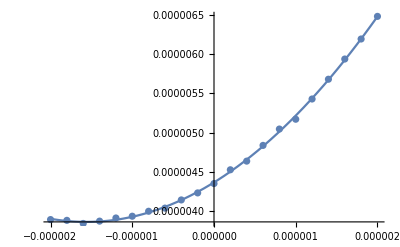

{x→-4.58351×10^-6}

{x→1.46054×10^-6}

```mathematica
f9cf15000=10^12{-2*10^-18,-1.8*10^-18,-1.6*10^-18,-1.4*10^-18,-1.2*10^-18,-1*10^-18,-8*10^-19,-6*10^-19,-4*10^-19,-2*10^-19,0.0,2*10^-19,4*10^-19,6*10^-19,8*10^-19,1*10^-18,1.2*10^-18,1.4*10^-18,1.6*10^-18,1.8*10^-18,2*10^-18};
f9cs15000={1.6019*10^-05,1.6042*10^-05,1.6069*10^-05,1.6133*10^-05,1.6193*10^-05,1.6294*10^-05,1.6399*10^-05,1.6543*10^-05,1.6713*10^-05,1.6881*10^-05,1.7092*10^-05,1.7331*10^-05,1.7564*10^-05,1.7831*10^-05,1.8144*10^-05,1.8461*10^-05,1.8799*10^-05,1.9135*10^-05,1.9526*10^-05,1.9922*10^-05,2.0355*10^-05};
f9n15000={72816,72526,71662,71933,72407,72376,73072,73166,74298,75155,76326,78323,79174,81371,83425,84030,86647,89090,91273,93315,95593};
f9cs15000f=f9cs15000*f9n15000/300000;
f9fit15000=FindFit[Transpose[{f9cf15000,f9cs15000f}],a x^2+b x+c,{a,b,c},x]
Show[Plot[a x^2+b x+c/. f9fit15000,{x,f9cf15000[[1]],f9cf15000[[21]]}],ListPlot[Transpose[{f9cf15000,f9cs15000f}]]]
Print[FindRoot[2==√2 √ll √((a x^2+b x+ c)Log[1+(a x^2+b x)/c]-(a x^2+b x))/.ll->10000000/.f9fit15000,{x,-0.1}]];
Print[FindRoot[2==√2 √ll √((a x^2+b x+ c)Log[1+(a x^2+b x)/c]-(a x^2+b x))/.ll->10000000/.f9fit15000,{x,0.1}]];
```